## Import Data From NetCDF

```mathematica
SetDirectory["/Users/penn/Documents/Code/Github/PhDThesis/data/SST"];
```

## Monthly Data

```mathematica
Import["sst.mnmean.nc"]
```

{lat,lon,sst,time,time_bnds}

```mathematica
mdata = Import["sst.mnmean.nc", {"Datasets", "sst"}];
```

```mathematica
Dimensions[mdata]
```

{415,180,360}

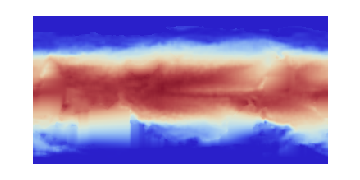

```mathematica
ArrayPlot[Reverse@mdata[[1,;;,;;]],ColorFunction->"ThermometerColors",ImageSize->Medium]
```

```mathematica
ListDensityPlot[Reverse@mdata[[1,;;,;;]]]
```

-Graphics-

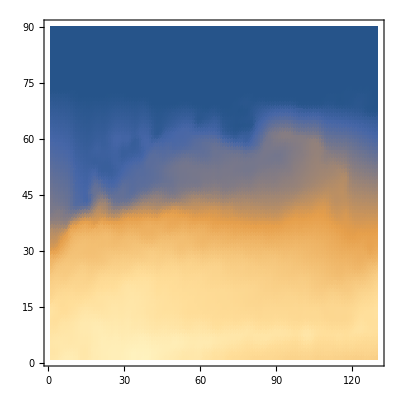

```mathematica
pacificmdata=mdata[[;;,1;;90,121;;250]];
Dimensions[pacificmdata];
ListDensityPlot[Reverse@pacificmdata[[1,;;,;;]]]
```

```mathematica
Reverse@{{1,2,3},{4,5,6}}
```

{{4,5,6},{1,2,3}}

## Weekly Data

```mathematica
Import["sst.wkmean.1981-1989.nc"]
```

{lat,lon,time,time_bnds,sst}

```mathematica
wdata1=Import["sst.wkmean.1981-1989.nc",{"Datasets","sst"}];
```

```mathematica
Dimensions[wdata1]
```

{427,180,360}

```mathematica
Import["sst.wkmean.1990-present.nc"]
```

{lat,lon,sst,time,time_bnds}

```mathematica
wdata2=Import["sst.wkmean.1990-present.nc",{"Datasets","sst"}]
```

Import::fmterr: Cannot import data as "NetCDF" format.

$Failed

## __________________________